## Half Normal Distribution.

I think this explains the spacing on some of the graphs from experiment one.

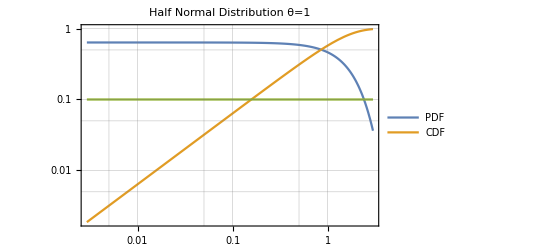

```mathematica
θ=1;
LogLogPlot[{(2 ⅇ^(-(x^2 θ^2)/π)θ)/π,Erf[(x θ)/(√π)],0.1},{x,0, 3},
PlotLegends->{"PDF","CDF"},
PlotLabel->StringForm["Half Normal Distribution θ=``",θ],
GridLines->Automatic,Frame->True]
```